# Hydrogen molecule: numerical integrations.

Definitions

```mathematica
ClearAll["Global`*"]
```

Definitions using Cartesian coordinates explicitly

```mathematica
Ra={0,-R/2,0};
Rb={0, R/2,0};
r1={x1,y1,z1};
r2={x2,y2,z2};
r1a=Sqrt[x1^2+(y1+R/2)^2+z1^2];
r1b=Sqrt[x1^2+(y1-R/2)^2+z1^2];
r2a=Sqrt[x2^2+(y2+R/2)^2+z2^2];
r2b=Sqrt[x2^2+(y2-R/2)^2+z2^2];
r12=Sqrt[(x1-x2)^2+(y1-y2)^2+(z1-z2)^2];
```

Defining one-electron orbitals

```mathematica
ϕ1a=1/Sqrt[Pi]*Exp[-r1a];
ϕ2a=1/Sqrt[Pi]*Exp[-r2a];
ϕ1b=1/Sqrt[Pi]*Exp[-r1b];
ϕ2b=1/Sqrt[Pi]*Exp[-r2b];
```

## Integrals

```mathematica
inf=5;
```

#### Overlap integral (1-electron)

```mathematica
s=NIntegrate[ϕ1a*ϕ1b, {x1, -inf, +inf}, {y1, -inf, inf}, {z1, -inf, inf}, Method->MultiDimensional, PrecisionGoal->2];
```

```mathematica
s=(1+R+1/3 R^2)Exp[-R];
```

```mathematica
fac=2*(1+s^2);
```

#### Coulomb integral (1-electron)

```mathematica
j=NIntegrate[ϕ1a*ϕ1a/r1b, {x1,-inf,inf}, {y1,-inf,inf}, {z1,-inf,inf},Method->MultiDimensional, PrecisionGoal->2];
```

```mathematica
j=1/R(1-(1+R)Exp[-2R]);
```

#### Overlap integral over r (1-electron)

```mathematica
k=NIntegrate[ϕ1b*ϕ1a/r1b, {x1,-inf, inf}, {y1, -inf, inf}, {z1, -inf, inf}, Method->MultiDimensional, PrecisionGoal->2];
```

```mathematica
k=(1+R)Exp[-R];
```

#### Some other fun integral (2-electron)

```mathematica
L:=NIntegrate[ϕ1a*ϕ1a*ϕ2b*ϕ2b/r12, {x1,-inf, inf}, {y1, -inf, inf}, {z1, -inf, inf}, {x2, -inf, inf}, {y2, -inf, inf}, {z2, -inf, inf}, Method->MonteCarlo, MaxPoints->10^6, PrecisionGoal->2]
```

```mathematica
M:=NIntegrate[ϕ1a*ϕ1b*ϕ2a*ϕ2b/r12,{x1,-inf, inf}, {y1, -inf, inf}, {z1, -inf, inf}, {x2, -inf, inf}, {y2, -inf, inf}, {z2, -inf, inf}, Method->MonteCarlo, MaxPoints->10^6, PrecisionGoal->2]
```

## Computing energies

```mathematica
E0:=-0.5
E1:=2*E0-2*j+L+1/R
E2:=2*E0*s^2-2*k*s+M+s^2/R
ET:=2*(E1+E2)/fac*27.2114
```

```mathematica
Table[{R, ET}, {R, 2.15,2.5, 0.05}]//Quiet
```

{{1.65,-34.1244},{1.7,-34.7599},{1.75,-35.1205},{1.8,-35.6039},{1.85,-35.9812},{1.9,-36.3905}}

## Fitting Morse potential function

{0.8505,-3.13498}

1.34281

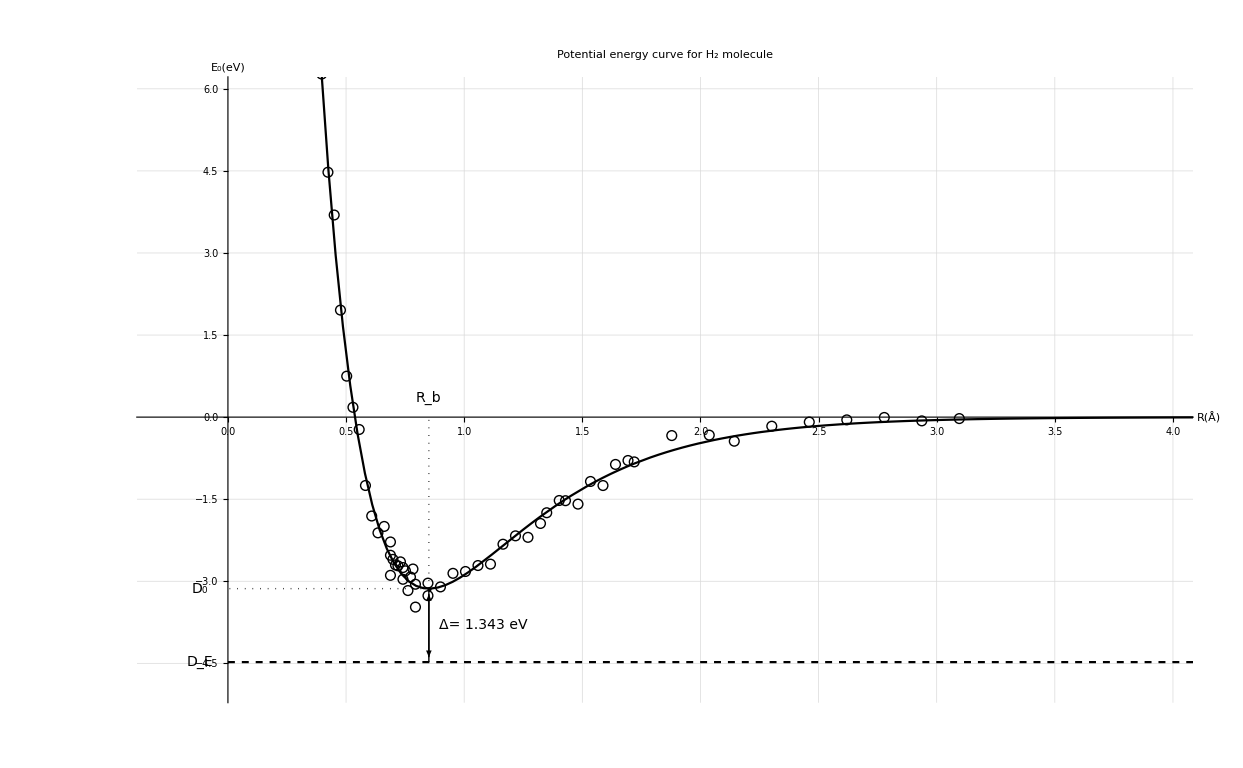

```mathematica
ClearAll["Global`*"];
data = Rest[Import[SystemDialogInput["FileOpen"]]];
D0exp = 4.4777954313;
H2unb=-27.211396132;
last=Last[data];
γb2A=0.52917725;
For[i=1,i<=Length[data],i++,
data[[i,1]]*=γb2A;
]
morse=a+b(Exp[-2*(x-c)/d]-2*Exp[-(x-c)/d]);
fit=FindFit[data,morse, {a, b, c, d}, x];
last = morse/.fit /.x-> 100;
For[i=1,i<=Length[data],i++,
data[[i,2]]-=last;
]
fit=FindFit[data,morse, {a, b, c, d}, x];
min=FindMinimum[morse/.fit, x];
minX=min[[2,1,2]];
minY=min[[1]];
min={minX,minY}
minPlot=Plot[minY, {x, 0, minX}, PlotStyle->{Dashed, Red}];
m=min[[1]];
morsePlot=Plot[morse/. fit, {x, -1, 100}, PlotStyle->Black,PlotRange->{{-1, 7},{-5,10}}, PlotStyle->Thick, Epilog->{PointSize[Large],Point[min],Dotted,Line[{min,{min[[1]],0}}],Line[{min,{0,min[[2]]}}],Text[Style["R_b",14],{min[[1]], 0.35}],Text[Style["D_0",14] ,{-.12, min[[2]]}],Text[Style["Δ= 1.343 eV",14]  ,{min[[1]]+0.23,(min[[2]] -D0exp)/2}],Text[Style["D_E",14],{-0.12, -D0exp}]}, PlotLabel->Style["Potential energy curve for H_2 molecule", 18],LabelStyle->{FontFamily->"Saab",13,GrayLevel[0]}];
pointPlot=ListPlot[data,PlotStyle->Black, PlotRange->{{0,7}, Automatic}, PlotMarkers->{"○",10}];
experiment=Plot[-D0exp, {x,0, 7}, PlotStyle->{Dashed, Black}];
diff=D0exp+minY
Show[morsePlot,experiment,pointPlot, Graphics[{Arrowheads[{{1,1,Graphics@Style[Text["►",{0,0},{0,0}],FontSize->12]}}],Arrow[{min,{min[[1]],-D0exp+0.09}}]}], Graphics[{Arrowheads[{{1,1,Graphics@Style[Text["►",{0,0},{0,0}],FontSize->12]}}],Arrow[{{min[[1]],-D0exp}, {min[[1]],min[[2]]-0.1}}]}],FrameLabel->{{Style["\!\(\*SubscriptBox[\(E\), \(0\)]\) [eV]"]},{Style["R [Å]"]}}, PlotRange->{{-0.3, 4},{-5,6}}, AxesLabel->{Style[HoldForm[R[Å]],18],Style[HoldForm[Subscript[Ε, 0][eV]],18]},FrameLabel->{{None,None},{None,None}},PlotLabel->Style[HoldForm[Potential energy curve for Subscript[H, 2] molecule],24],LabelStyle->{FontFamily->"URW Gothic L",GrayLevel[0]},AxesStyle->Thick,PlotRange->{{-0.3, 4},{-5,6}},ImagePadding->70,TicksStyle-> 16, GridLines->Automatic]
```

```mathematica
DistributionFitTest[data,{morse, {a, b, c, d}}];
```

DistributionFitTest::rctnlndst: The argument {a + b\ (-2\ ⅇ^c + Times[« 2 »]/d + ⅇ^-2\ (-c + x)/d), {a, b, c, d}} at position 2 should be a valid distribution or a rectangular array of real numbers with length greater than the dimension of the array. The dimensionality of the arguments at positions 1 and 2 must match.

```mathematica
Clear[a]
```

```mathematica
Clear[a,b,c,d]
```

```mathematica
fm=NonlinearModelFit[data,morse, {a, b, c, d}, x]
```

FittedModel[-3.0339×10^-11+3.13498 (-2 ⅇ^(2.21288 (0.8505-x))+ⅇ^(-4.42577 (-«19»+x)))]

```mathematica
%212["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -3.0339×10^-11 | 0.0651632 | -4.65584×10^-10 | 1
b | 3.13498 | 0.083575 | 37.511 | 2.50897×10^-39
c | 0.8505 | 0.00559235 | 152.083 | 1.46184×10^-70
d | 0.451899 | 0.00837437 | 53.9621 | 2.47251×10^-47

## Plotting orbitals

```mathematica
R=0.8505001372688124;
z1=0;
int=NIntegrate[(ϕ1a+ϕ1b)^2, {x1, -inf, inf},{y1, -inf, inf}, Method->MultiDimensional, PrecisionGoal->2]
```

1.85285

```mathematica
orb1=ContourPlot3D[{ϕ1a,ϕ1b},{x1,-5,5},{y1,-5,5},{z1,-5,5}, PerformanceGoal->"Speed",Contours->3, PlotTheme->"Minimal", ContourStyle->Directive[Opacity[0.6]], BoundaryStyle->Red, AxesLabel->{"x","y","z"}, ColorFunction->ColorData[1]];
orb2=ContourPlot3D[{(ϕ1a+ϕ1b)^2},{x1,-5,5},{y1,-5,5},{z1,-5,5}, PerformanceGoal->"Speed",Contours->3, PlotTheme->"Detailed", ContourStyle->Directive[Opacity[0.4]], BoundaryStyle->Red, AxesLabel->{"x","y","z"},ColorFunction->"SunsetColors"];
orb3=ContourPlot3D[{(ϕ1a-ϕ1b)^2},{x1,-5,5},{y1,-5,5},{z1,-5,5}, PerformanceGoal->"Speed",Contours->3, PlotTheme->"Detailed", ContourStyle->Directive[Opacity[0.4]], BoundaryStyle->Red, AxesLabel->{"x","y","z"}, ColorFunction->"TemperatureMap"];
tab=Table[{orb1, orb2, orb3}, {i,1,1}];
GraphicsGrid[Partition[tab, 1], ImageSize->Full]
```

```mathematica
z1=0;
contours:=Partition[Table[ContourPlot[(ϕ1a-ϕ1b)^2, {x1,-5,5},{y1,-5,5}, PlotLabel->Style[R, 10] ,PerformanceGoal->"Quality",FrameLabel->{"x","y"}, Background-> White,ColorFunction->"SunsetColors",PlotPoints->50, PlotRange->All,Contours->8],{R,0.8,4, 0.2}],3] ;
densities:=Partition[Table[DensityPlot[(1/int)*(ϕ1a-ϕ1b)^2, {x1,-5,5},{y1,-5,5}, PlotLabel->Style[R, 16] ,FrameLabel->{"x","y"}, ColorFunction->"SunsetColors", PlotRange->All, Mesh->True,PerformanceGoal->"Quality",PlotPoints->{160,160}, PlotLabel->True],{R,0.8,4, 0.2}],3] ;
```

```mathematica
Clear[R];
```

```mathematica
Labeled[orbs=GraphicsGrid[densities,Frame->None, Background->White, Spacings->Scaled[.01], ImageSize->Full], DensityPlot[y,{y,0,.345},{x,0,1},AspectRatio->0.07,ColorFunction->"SunsetColors",FrameTicks->{{None,None},{Automatic,None}},FrameStyle->GrayLevel[0.6],FrameTicksStyle->GrayLevel[0.],ImageSize->First@AbsoluteCurrentValue[grid,ImageSize],Mesh->False,PlotRangePadding->0]]
```

```mathematica
Export["orbs"<>#,%108, ImageResolution->600]&/@{".pdf"}
```

{orbs.pdf}

```mathematica
ContourPlot[(1/int)*(ϕ1a+ϕ1b)^2, {x1,-5,5},{y1,-5,5}, PlotLabel->Style[R, 16] ,FrameLabel->{"x","y"}, ColorFunction->"SunsetColors", PlotRange->All, Mesh->True,PerformanceGoal->"Quality",PlotPoints->{120,120}, PlotLabel->True,PlotLegends->True]
```

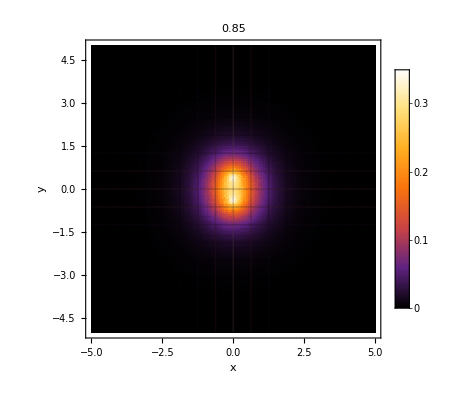

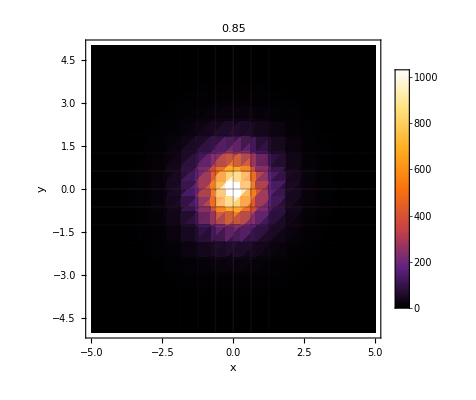

```mathematica
DensityPlot[0.5*int^2, {x1,-5,5},{y1,-5,5}, PlotLabel->Style[R, 16] ,FrameLabel->{"x","y"}, ColorFunction->"SunsetColors", PlotRange->All, Mesh->True,PerformanceGoal->"Speed",PlotPoints->{20,20}, PlotLabel->True,PlotLegends->True]
DensityPlot[0.5*(ϕ1a+ϕ1b)^2, {x1,-5,5},{y1,-5,5}, PlotLabel->Style[R, 16] ,FrameLabel->{"x","y"}, ColorFunction->"SunsetColors", PlotRange->All, Mesh->True,PerformanceGoal->"Speed",PlotPoints->{20,20}, PlotLabel->True,PlotLegends->True]
```

```mathematica
Export["orbs"<>#,orbs, ImageResolution->600]&/@{".pdf"}
```

## Plotting functions

```mathematica
ϕ2a
```

(ⅇ^(-√(x2^2+(R/2+y2)^2+z2^2)))/(√π)

```mathematica
Clear[x1]
z1=0;
R=0.8505001372688124;
inf=2.5;
```

```mathematica
w1=Plot3D[{((ⅇ^(-√(Subscript[x, 1]^2+(R/2+Subscript[y, 1])^2+z1^2)))/(√π)+(ⅇ^(-√(Subscript[x, 1]^2+(-R/2+Subscript[y, 1])^2+z1^2)))/(√π))^1*1.1398230685795743}, {Subscript[y, 1],-inf,inf}, {Subscript[x, 1],-inf,inf},PlotStyle->Black,PlotRange->Full,PlotLabel->Style["ψ_+-state",18],AxesLabel->{Style["x_1",20],None},ColorFunction->"SunsetColors",MeshFunctions->{#3&},Mesh->5,Mesh->None,NormalsFunction->Function[{x,y,z},RandomReal[{0,1},{3}]], Boxed->False,PerformanceGoal->"Quality",PlotPoints->30,Axes->True];
w2=Plot3D[{1/0.13333844356027663*((ⅇ^(-√(Subscript[x, 1]^2+(R/2+Subscript[y, 1])^2+z1^2)))/(√π)-(ⅇ^(-√(Subscript[x, 1]^2+(-R/2+Subscript[y, 1])^2+z1^2)))/(√π))^2}, {Subscript[y, 1],-inf,inf},{Subscript[x, 1],-inf,inf}, PlotRange->Full,PlotLabel->Style["ψ_--state",18],AxesLabel->{Style["x_1",20],None},ColorFunction->"SunsetColors",MeshFunctions->{#3&},Mesh->5,Mesh->None,NormalsFunction->Function[{x,y,z},RandomReal[{0,1},{3}]],Boxed->False,PerformanceGoal->"Quality",PlotPoints->30];
GraphicsGrid[{{w1,w2}},Frame->None, Background->White, Spacings->Scaled[.01], ImageSize->Full,Frame->False]
```

-Graphics-

```mathematica
Export["wfs"<>#,%588, ImageResolution->600]&/@{".pdf"}
```

{wfs.pdf}

## Hartree-Fock treatment

{-4.0639,0.687934}

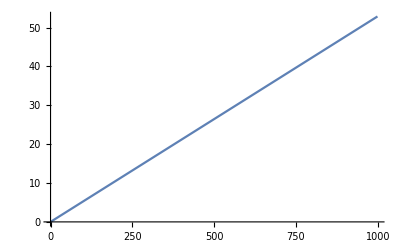

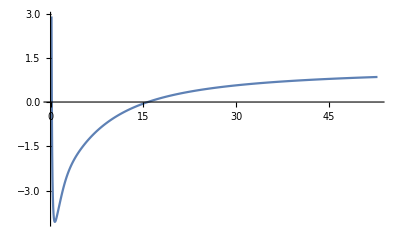

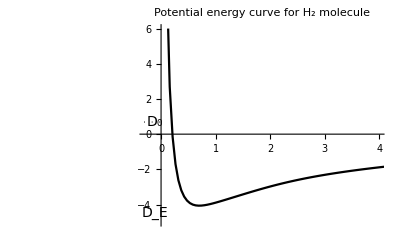

```mathematica
twohen=27.2116;
conv=4.477954313/31.9570;
bohrtoA=0.52918;
D0exp=4.4777954313;
data=Import["/home/patlip/Dokumenty/H2/code/HF/Hartree-Fock/h2.out","Table"];
dataLength=Length[data];
R=Range[dataLength-1];
Eelec=Range[dataLength-1];
Enuc=Range[dataLength-1];
Etot=Range[dataLength-1];
Ebind=Range[dataLength-1];
For[i=1,i<dataLength,i++,R[[i]]=data[[i,1]];
Eelec[[i]]=data[[i,2]];
Enuc[[i]]=data[[i,3]];
Etot[[i]]=data[[i,4]];
Ebind[[i]]=data[[i,5]];]
npoints=(Floor[.1*dataLength]);
line=Transpose[{R,Etot-Last[Etot]}][[-npoints;;]];
fit=Fit[line,{1,x},x];
(*Show[ListPlot[line,PlotStyle->Red],Plot[fit,{x,line[[1,1]],line[[npoints-1,1]]}]]*)
For[i=1,i<dataLength,i++,R[[i]]=bohrtoA*data[[i,1]];
Eelec[[i]]=data[[i,2]];
Enuc[[i]]=data[[i,3]];
Etot[[i]]=((data[[i,4]]));
Ebind[[i]]=conv*data[[i,5]];]
min={Min[Ebind],R[[Position[Ebind,Min[Ebind]][[1,1]]]]}
p1=ListLinePlot[R]
p2=ListLinePlot[Transpose[{R,Eelec}]];
p3=ListLinePlot[Transpose[{R,Enuc}]];
p4=ListLinePlot[Transpose[{R,Etot}]];
p5=ListLinePlot[Transpose[{R,Ebind}]]
energyPlot=ListLinePlot[Transpose[{R,Ebind}],PlotStyle->Black,PlotRange->{{-0.3,4},{-5,6}},PlotStyle->Thick,Epilog->{PointSize[Large],Point[min],Dotted,Line[{min,{min[[1]],0}}],Line[{min,{0,min[[2]]}}],Text[Style["\!\(\*SubscriptBox[\(R\), \(b\)]\)",14],{min[[1]],0.35}],Text[Style["\!\(\*SubscriptBox[\(D\), \(0\)]\)",14],{-.12,min[[2]]}],Text[Style["Δ= 1.343 eV",14],{min[[1]]+0.23,(min[[2]]-D0exp)/2}],Text[Style["\!\(\*SubscriptBox[\(D\), \(E\)]\)",14],{-0.12,-D0exp}]},PlotLabel->Style["Potential energy curve for \!\(\*SubscriptBox[\(H\), \(2\)]\) molecule",18],LabelStyle->{FontFamily->"Saab",13,GrayLevel[0]}]
```

ReplaceAll::reps: {-0.219061} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-0.214579} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

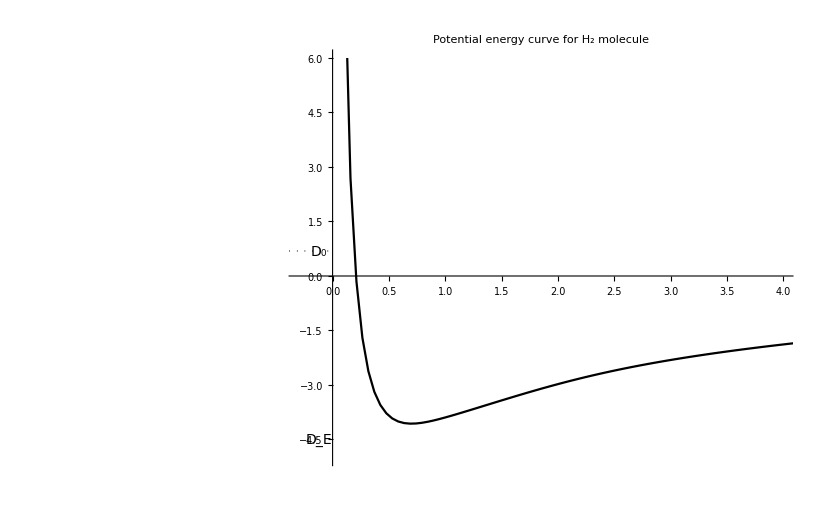

```mathematica
morsePlot=Plot[morse/. fit, {x, -1, 100}, PlotStyle->Black,PlotRange->{{-1, 7},{-5,10}}, PlotStyle->Thick, Epilog->{PointSize[Large],Point[min],Dotted,Line[{min,{min[[1]],0}}],Line[{min,{0,min[[2]]}}],Text[Style["R_b",14],{min[[1]], 0.35}],Text[Style["D_0",14] ,{-.12, min[[2]]}],Text[Style["Δ= 1.343 eV",14]  ,{min[[1]]+0.23,(min[[2]] -D0exp)/2}],Text[Style["D_E",14],{-0.12, -D0exp}]}, PlotLabel->Style["Potential energy curve for H_2 molecule", 18],LabelStyle->{FontFamily->"Saab",13,GrayLevel[0]}];
Show[energyPlot,morsePlot]
```

```mathematica
morse/. fit
```

ReplaceAll::reps: {-0.216891 + 0.00217466\ x} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

a+b (-2 ⅇ^((c-x)/d)+ⅇ^(-(2 (-c+x))/d))/.-0.216891+0.00217466 x

```mathematica
fit
```

-0.216891+0.00217466 x